```mathematica
JoukowskyTransform[z_,λ_]:=z+λ^2/z;
InverseJoukowskyTransform[w_,λ_]:=If[Re[w]<=0,1/2 (w+√(-4 λ^2+w^2)),1/2 (w-√(-4 λ^2+w^2))];
ComplexPotential[z_,Γ_,R_,V_]:=V(z+R^2/z)-I Γ/(2π)Log[z];
ComplexVelocity[z_,z0_,r_,Γ_,V_,α_]:=Conjugate[V E^(-I α)+(I Γ)/(2Pi (z-z0))-(V R^2 E^(I α))/(z-z0)^2];
imageCurve[t_]:=JoukowskyTransform[z0+r ⅇ^(ⅈ t),λ];
{z0,V,α}={0.2+0.1I,100,0};(*圆心,均匀流速,攻角*)
{r,λ,Γ,R}={Norm[1-z0],1,4π V R Sin[α+ArcSin[Im[z0]/R]] ,r};(*圆半径，Joukowsky变换参数，流参数（由Kutta条件），半径*)
```

```mathematica
circlePlot=ParametricPlot[ReIm[z0+r ⅇ^(ⅈ t)],{t,0,2 Pi},PlotStyle->Red];
airfoilPlot=ParametricPlot[ReIm[imageCurve[t]],{t,0,2 Pi},PlotStyle->Red];
```

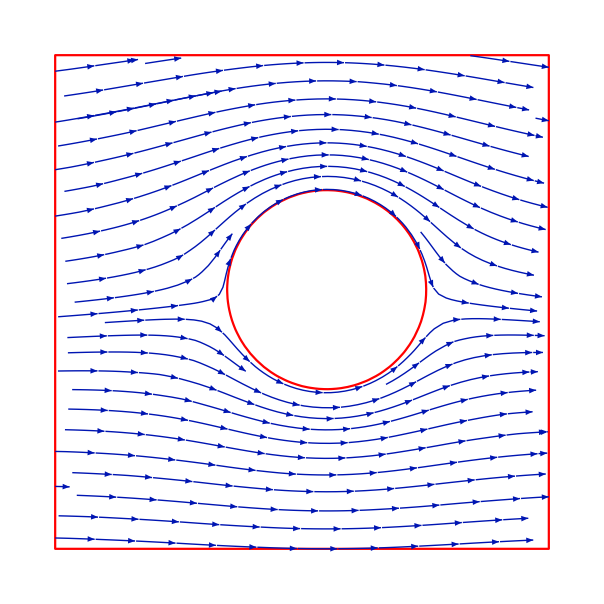

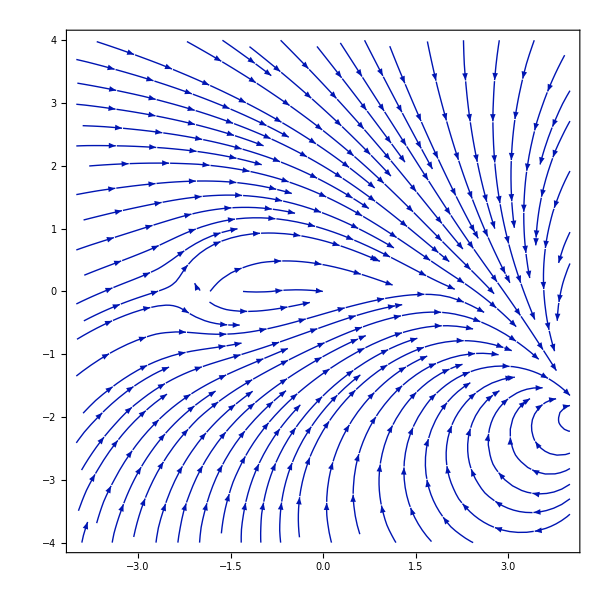

```mathematica
circleStreamPlot=StreamPlot[ReIm@ComplexVelocity[x+I y,z0,r,Γ,V,α],{x,-2,2},{y,-2,2},RegionFunction->Function[{x,y,vx,vy,n},Norm[x+I y-z0]>=r],RegionFillingStyle->None,RegionBoundaryStyle->Red,Frame->False]
airfoilStreamPlot=StreamPlot[ReIm[ComplexVelocity[InverseJoukowskyTransform[x+I y,λ],z0,r,Γ,V,α]/Conjugate[1-λ^2/(InverseJoukowskyTransform[x+I y,λ])^2]],{x,-4,4},{y,-4,4}]
```

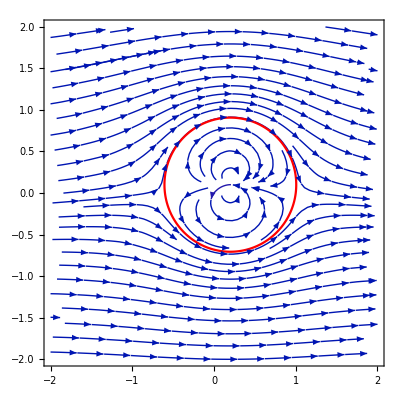

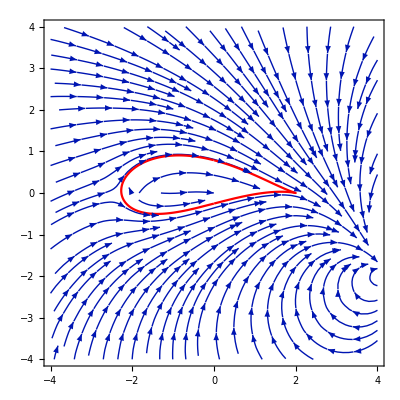

```mathematica
Show[circleStreamPlot,circlePlot]
Show[airfoilStreamPlot,airfoilPlot]
```

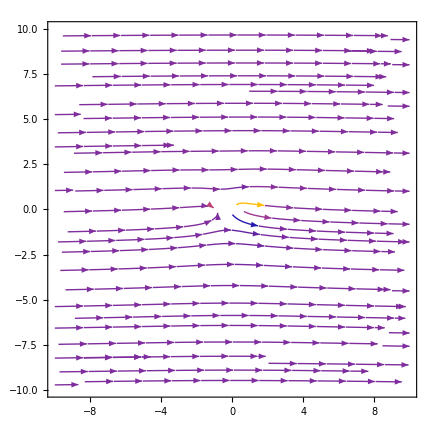

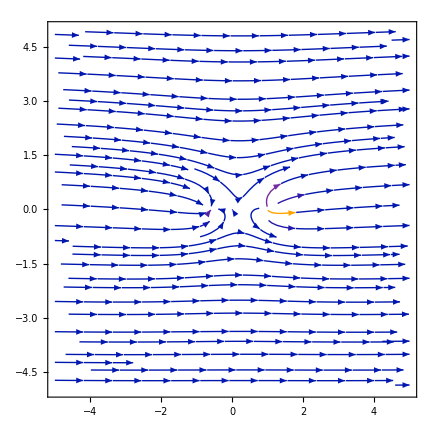

```mathematica
StreamPlot[ReIm[ComplexVelocity[x+I y,z0,r,Γ,V,α]/Conjugate[1-λ^2/(x+I y)^2]],{x,-10,10},{y,-10,10},Axes->True]
StreamPlot[ReIm[InverseJoukowskyTransform[ComplexVelocity[x+I y,z0,r,Γ,V,α],λ]],{x,-5,5},{y,-5,5},Axes->True]
```

```mathematica
ComplexPotential[x+I y,Γ,R,V]
```

100 (x+0.65/(x+ⅈ y)+ⅈ y)+(0.+20. ⅈ) Log[x+ⅈ y]

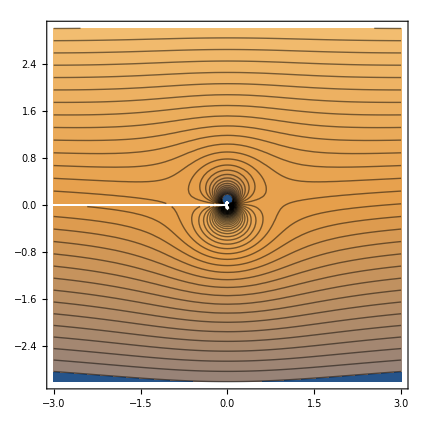

```mathematica
ContourPlot[Im[ComplexPotential[x+I y,Γ,R,V]],{x,-3,3},{y,-3,3},Contours->50]
```

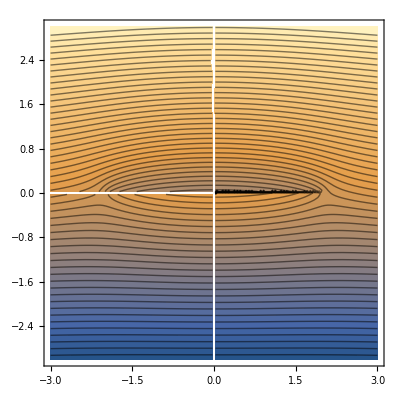

100 (x+1/(x+ⅈ y)+0.65/(x+1/(x+ⅈ y)+ⅈ y)+ⅈ y)+(0.+20. ⅈ) Log[x+1/(x+ⅈ y)+ⅈ y]

```mathematica
ContourPlot[Im[ComplexPotential[InverseJoukowskyTransform[x+I y,λ],Γ,R,V]],{x,-3,3},{y,-3,3},Contours->50]
```